# Rock heterogeneities & fractures

## How toughness heterogeneities affect the propagation of fluid driven fractures

Mathematica Notebook created by Carlo Peruzzo on Tuesday 26th October 2020
EPFL ENAC IIC GEL
GC B1 385 (Bâtiment GC)
Station 18, 1015 Lausanne, Switzerland
Phone: +41 (0)21 693 76 47
carlo.peruzzo@epfl.ch
Geo-energy Laboratory EPFL

contributors:
Brice Lecampion - brice.lecampion@epfl.ch
Judith Capron - judith.capron@epfl.ch

version n.: 0.0.1

#### Formatting the way of plotting

```mathematica
(*http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
(*ResourceFunction["MaTeXInstall"][];*) (* <-Run  once forevere *) 
Needs["MaTeX`"]
Myfontsize=22;
texStyle={FontFamily->"CMU Serif",FontSize->Myfontsize};
SetOptions[Plot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[LogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLinearPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLogLogPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListVectorPlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
SetOptions[ListLinePlot,Frame-> True,ImageSize-> 700,FrameStyle->Directive[Black],BaseStyle->texStyle];
```

#### Installing the post-processing module of PyFrac

```mathematica
(*PacletUninstall["PyFrac_post"]*)
PacletInstall["/Users/carloperuzzo/Desktop/toughness_jump/mmaNb/PyFracPost-0.0.1.paclet"]
```

PacletObject[…]

```mathematica
Needs["PostprocessPyFrac`"]
```

getFr::shdw: Symbol getFr appears in multiple contexts {getSINGLEfrac`,getDOUBLEfrac`}; definitions in context getSINGLEfrac` may shadow or be shadowed by other definitions.

## Importing & processing the numerical data for multiple simulations

#### Defining paths to the json files

```mathematica
commonPath = "/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_";
PathNameSimResults=StringJoin[commonPath,#]&/@{"1p8_export.json","3p6_export.json"}
```

{/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_1p8_export.json,/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_3p6_export.json}

#### Processing each simulation to get the results

```mathematica
SimProcessed = ParallelMap[postProcessPyfrac[#,"single_fracture"]&,PathNameSimResults]
```

{<|Simpath→/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_1p8_export.json,11,pf_B(t)→{{0.0000910421,0.},{0.0000983356,-9.07886×10^6},{0.000106213,1.43696×10^7},11,{0.000262173,2.58655×10^7},{0.000278616,2.57102×10^7},{0.0003,2.54971×10^7}}|>,<|1|>}
 |  |  |  |

```mathematica
Keys[SimProcessed[[1]]]
```

{Simpath,SingleFractures,times,xinj,yinj,rRightVsT,rLeftVsT,rUpVsT,rBottomVsT,LastMesh,w_A(t),pf_A(t),pf_B(t)}

### Plotting the internal radius

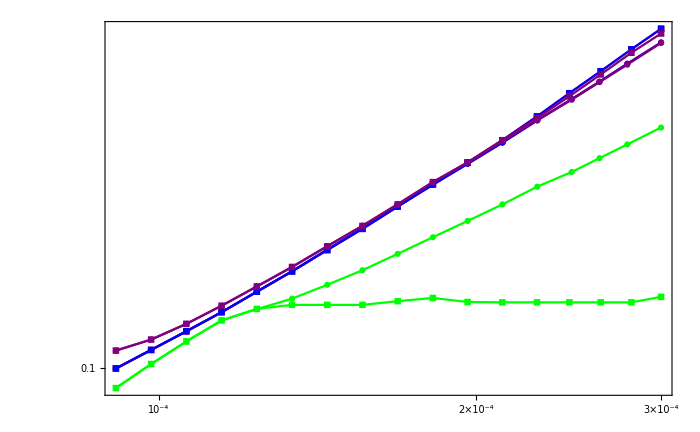

```mathematica
(* get the data *)
rRightVsT=#["rRightVsT"] &/@SimProcessed;
rUpVsT=#["rUpVsT"] &/@SimProcessed;
rBottomVsT=#["rBottomVsT"] &/@SimProcessed;
rLeftVsT=#["rLeftVsT"] &/@SimProcessed;

(* plot *)
xlabel=MaTeX["t \\text{ [s]}",FontSize->Myfontsize];
ylabel=MaTeX["R\\textsubscript{-} \\text{ [m]}",FontSize->Myfontsize];
Show[
ListLogLogPlot[rRightVsT,Joined->True,PlotStyle->Green,PlotLegends->{MaTeX["\\text{num } R\\textsubscript{right} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],

ListLogLogPlot[rUpVsT,Joined->True,PlotStyle->Red,PlotLegends->{MaTeX["\\text{num } R\\textsubscript{up} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],

ListLogLogPlot[rBottomVsT,Joined->True,PlotStyle->Blue,PlotLegends->{MaTeX["\\text{num } R\\textsubscript{bottom} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],

ListLogLogPlot[rLeftVsT,Joined->True,PlotStyle->Purple,PlotLegends->{MaTeX["\\text{num } R\\textsubscript{left} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],
FrameLabel->{xlabel,ylabel},PlotRange->All]

(*LogLogPlot[RM[t,1],{t,0.00008,0.0003},PlotStyle->{Black,Dashed},PlotLegends->LineLegend[{MaTeX["\\text{M - radial solution (1st order)}",FontSize->Myfontsize-2]}]]*)
```

### Plotting w(t) at point A

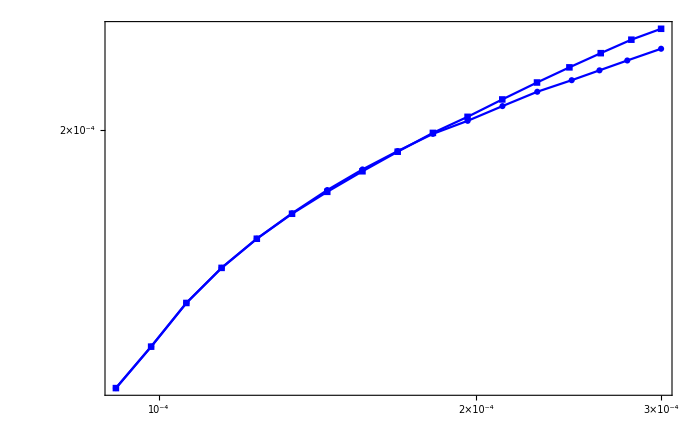

```mathematica
(* get the data *)
data=#["w_A(t)"] &/@SimProcessed;

(* plot *)
xlabel=MaTeX["t \\text{ [s]}",FontSize->Myfontsize];
ylabel=MaTeX["w\\textsubscript{A} \\text{ [mm]}",FontSize->Myfontsize];

Show[
ListLogLogPlot[data,Joined->True,PlotStyle->Blue,PlotLegends->{MaTeX["\\text{num fracture opening: } w\\textsubscript{A} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],

FrameLabel->{xlabel,ylabel},PlotRange->All]

(*LogLogPlot[ wM[0.,t,1],{t,0.05,3.9},PlotStyle->{Black,Dashed},PlotLegends->LineLegend[{MaTeX["\\text{M - radial solution (1st order)}",FontSize->Myfontsize-2]}]]*)
```

### Plotting pf(t) at point A

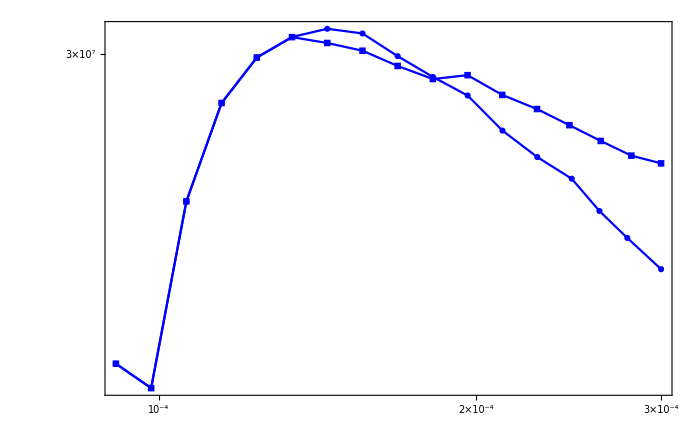

```mathematica
(* get the data *)
data=#["pf_A(t)"] &/@SimProcessed;

(* plot *)
xlabel=MaTeX["t \\text{ [s]}",FontSize->Myfontsize];
ylabel=MaTeX["p\\textsubscript{f A} \\text{ [MPa]}",FontSize->Myfontsize];

Show[
ListLogLogPlot[data,Joined->True,PlotStyle->Blue,PlotLegends->{MaTeX["\\text{num fluid pressure: } p\\textsubscript{f A} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],FrameLabel->{xlabel,ylabel},PlotRange->All]

(*LogLogPlot[10^-6 pM[0.,t,1],{t,0.05,3.9},PlotStyle->{Black,Dashed},PlotLegends->LineLegend[{MaTeX["\\text{M - radial solution (1st order)}",FontSize->Myfontsize-2]}]]*)
```

### Plotting pf(t) at point B

```mathematica
(* get the data *)
data=#["pf_B(t)"] &/@SimProcessed;

(* plot *)
xlabel=MaTeX["t \\text{ [s]}",FontSize->Myfontsize];
ylabel=MaTeX["p\\textsubscript{f B} \\text{ [MPa]}",FontSize->Myfontsize];

Show[ListLogLogPlot[data,Joined->True,PlotStyle->Blue,PlotLegends->{MaTeX["\\text{num fluid pressure: } p\\textsubscript{f B} ",FontSize->Myfontsize-2]},PlotMarkers->Automatic],FrameLabel->{xlabel,ylabel},PlotRange->All]
```

## Importing & processing the numerical data for a single simulation

### Plotting the footprints

```mathematica
PathNameSimResult=PathNameSimResults[[1]]
```

/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_1p8_export.json

```mathematica
NUMdata01=Import[PathNameSimResult,"RawJSON"];
Keys[NUMdata01]
```

{simul_info,time_srs_of_Fr_list,Fr_list,Number_of_fronts,mesh_info,w_at_my_point,time_list_W_at_my_point,pf_at_my_point_A,time_list_pf_at_my_point_A,pf_at_my_point_B,time_list_pf_at_my_point_B,w_vert_slice_,pf_horiz_slice_,ux_horizontal_y0_value,ux_horizontal_y0_time,ux_horizontal_y0_coord,uy_vertical_x0_value,uy_vertical_x0_time,uy_vertical_x0_coord,w,p,info_for_w_and_p}

```mathematica
(*The data for the velocity is bit heavy and it has to be loaded from a separate file*)
PathNameSimulationResultVEL="/Users/carloperuzzo/PyFrac_git/toughness_jump/Data/toughness_heterog_1p8_VEL_as_vector.json";NUMdataVEL01=Import[PathNameSimulationResultVEL,"RawJSON"];
Keys[NUMdataVEL01]
```

{vel_list,vel_times,mesh_info}

```mathematica
Sim=SimProcessed[[1]];
Keys[Sim]
```

{Simpath,SingleFractures,times,xinj,yinj,rRightVsT,rLeftVsT,rUpVsT,rBottomVsT,LastMesh,w_A(t),pf_A(t),pf_B(t)}

```mathematica
Keys[Sim["LastMesh"]]
```

{hx,hy,Nelts,vertexes,conn,centers,Neighbors}

```mathematica
bckground= Graphics[{EdgeForm[{Thin,LightGray}],Transparent,GraphicsComplex[Sim["LastMesh"]["vertexes"],Polygon[Sim["LastMesh"]["conn"][[1;;]] ] ]}]
```

-Graphics-

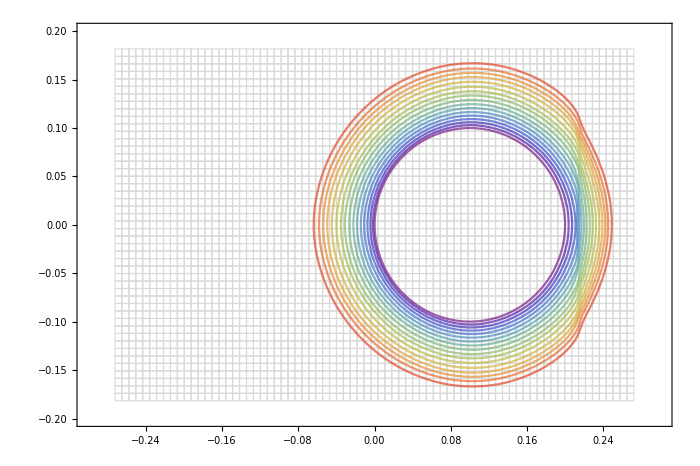

```mathematica
SingleFracture=Sim["SingleFractures"];
TimeList=Sim["times"];
chosentimes=Range[1,Length[TimeList],1];(*<<<plot each 3 time steps*)(*chosentimes=Range[Length[TimeList]];*)Legendi=Round[TimeList[[chosentimes]],0.0001];
xlabel=MaTeX["x \\text{ [mm]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [mm]}",FontSize->Myfontsize];
opt={Frame->True,AspectRatio->Automatic,PlotRange->{{-0.3,0.3},{-0.2,0.2}},FrameLabel->{xlabel,ylabel},ImageSize->700,FrameStyle->Directive[Black],BaseStyle->texStyle};

optlegend={PlotLegends->LineLegend["Rainbow",MaTeX[#,FontSize->Myfontsize-2]&/@Legendi,LegendLabel->Column@MaTeX[{"\\text{Numerical data:}","\\text{(time [s])}"},FontSize->Myfontsize]]};


selectedFracturesTotal=SingleFracture[[chosentimes]];
Superposition=Show[bckground,ListPlot[selectedFracturesTotal,Joined->True,optlegend,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/Length[selectedFracturesTotal]]}],opt]
```

### Plotting w(y,t) along a slice

```mathematica
dataVslice01=NUMdata01["w_vert_slice_"];(*data concerning the vertical section*)dataVsliceNoF01=NUMdata01["Number_of_fronts"][[1]];(*number of fronts per each time*)indxCOAL01=Position[dataVsliceNoF01,1][[1]][[1]];(*index of the coalescence time*)NoTmStpsVsl01="size_of_data"/.dataVslice01;(*number of slices*)TmLstVsl01="time_list"/.dataVslice01;(*times for each slice*)SamplingCoordListVsl01=Table["w_sampling_coords_"<>ToString[i]/.dataVslice01,{i,0,NoTmStpsVsl01-1}];


timesfromcoal=TmLstVsl01-TmLstVsl01[[indxCOAL01]];
TimeSlicingwOFx01=Position[timesfromcoal,_?(#>0&)]//Flatten;
NoTimeSlicwOFx01=Length[TimeSlicingwOFx01];
```

```mathematica
xandyTOxy[list1_,list2_]:=Module[{i},Table[{list1[[i]],list2[[i]]},{i,1,Length[list1]}]]
LegendwOFx01=MaTeX[#,FontSize->Myfontsize-2]&/@Round[TmLstVsl01[[TimeSlicingwOFx01]]-TmLstVsl01[[indxCOAL01]],0.000001];
xlabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["w \\text{ [mm]}",FontSize->Myfontsize];
NUMwOFx01=Table[i=TimeSlicingwOFx01[[j]];xandyTOxy[SamplingCoordListVsl01[[i]],"w_"<>ToString[i-1]/.dataVslice01],{j,1,NoTimeSlicwOFx01}];
plotNUMwOFx01=ListLinePlot[NUMwOFx01,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/NoTimeSlicwOFx01]},PlotLegends->LineLegend[LegendwOFx01,LegendLabel->MaTeX["\\text{Numerical data [s]:}",FontSize->Myfontsize]],FrameLabel->{xlabel,ylabel},PlotMarkers->{"◦"}]
```

-Graphics-

### Plotting pf(x,t) along a slice

```mathematica
dataHslice01=NUMdata01["pf_horiz_slice_"];(*data concerning the vertical section*)dataHsliceNoF01=NUMdata01["Number_of_fronts"][[1]];(*number of fronts per each time*)indxCOAL01=Position[dataHsliceNoF01,1][[1]][[1]];(*index of the coalescence time*)NoTmStpsHsl01="size_of_data"/.dataHslice01;(*number of slices*)TmLstHsl01="time_list"/.dataHslice01;(*times for each slice*)SamplingCoordListHsl01=Table["pf_sampling_coords_"<>ToString[i]/.dataHslice01,{i,0,NoTmStpsHsl01-1}];


timesfromcoal=TmLstHsl01-TmLstHsl01[[indxCOAL01]];
TimeSlicingpfOFx01=Range[1,Length[timesfromcoal],5];
NoTimeSlicpfOFx01=Length[TimeSlicingpfOFx01];
```

```mathematica
xandyTOxy[list1_,list2_]:=Module[{i},Table[{list1[[i]],list2[[i]]},{i,1,Length[list1]}]]
LegendpfOFx01=MaTeX[#,FontSize->Myfontsize-2]&/@Round[TmLstHsl01[[TimeSlicingpfOFx01]]-TmLstHsl01[[indxCOAL01]],0.000001];
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["pf \\text{ [MPa]}",FontSize->Myfontsize];
NUMpfOFx01=Table[i=TimeSlicingpfOFx01[[j]];xandyTOxy[SamplingCoordListHsl01[[i]],"pf_"<>ToString[i-1]/.dataHslice01],{j,1,NoTimeSlicpfOFx01}];
plotNUMpfOFx01=ListLinePlot[NUMpfOFx01,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/NoTimeSlicpfOFx01]},PlotLegends->LineLegend[LegendpfOFx01,LegendLabel->MaTeX["\\text{Numerical data [s]:}",FontSize->Myfontsize]],FrameLabel->{xlabel,ylabel},PlotMarkers->{"◦"}]
```

-Graphics-

### Comparison of v_x(x,y=0)

```mathematica
uxHsliceVAL=NUMdata01["ux_horizontal_y0_value"];
uxHsliceCOOR=NUMdata01["ux_horizontal_y0_coord"];
uxHsliceTIME=NUMdata01["ux_horizontal_y0_time"];
sizeOfdata=Length[uxHsliceVAL];

(*subset of times*)
chosentimes=Range[10,Length[TimeList],4];(*<<<plot each 3 time steps*)uxHsliceVAL=uxHsliceVAL[[chosentimes]];
uxHsliceCOOR=uxHsliceCOOR[[chosentimes]];
uxHsliceTIME=uxHsliceTIME[[chosentimes]];
sizeOfdata=Length[uxHsliceVAL];
```

```mathematica
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["u\\textsubscript{x} \\text{ [m/s]}",FontSize->Myfontsize];
LegenduxOFx01=MaTeX[#,FontSize->Myfontsize-2]&/@Round[uxHsliceTIME,0.00001];

uxTOplot=Table[ux=uxHsliceVAL[[i]];uxcoor=uxHsliceCOOR[[i]];Table[{uxcoor[[j]],ux[[j]]},{j,1,Length[ux]}],{i,1,sizeOfdata}];
ListPlot[uxTOplot,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/sizeOfdata]},FrameLabel->{xlabel,ylabel},Joined->True,PlotRange->All,PlotMarkers->{"◦"},PlotLegends->LineLegend[LegenduxOFx01,LegendLabel->MaTeX["\\text{Numerical data [s]:}",FontSize->Myfontsize]]]
```

-Graphics-

### Comparison of v_y(x=0,y)

```mathematica
uyVsliceVAL=NUMdata01["uy_vertical_x0_value"];
uyVsliceCOOR=NUMdata01["uy_vertical_x0_coord"];
uyVsliceTIME=NUMdata01["uy_vertical_x0_time"];
sizeOfdata=Length[uyVsliceVAL];

(*subset of times*)
chosentimes=Range[10,Length[TimeList],4];(*<<<plot each 3 time steps*)uyVsliceVAL=uyVsliceVAL[[chosentimes]];
uyVsliceCOOR=uyVsliceCOOR[[chosentimes]];
uyVsliceTIME=uyVsliceTIME[[chosentimes]];
sizeOfdata=Length[uxHsliceVAL];
```

```mathematica
xlabel=MaTeX["y \\text{ [m] }",FontSize->Myfontsize];
ylabel=MaTeX["u\\textsubscript{y} \\text{ [m/s]}",FontSize->Myfontsize];
LegenduyOFy01=MaTeX[#,FontSize->Myfontsize-2]&/@Round[uyVsliceTIME,0.000001];

uyTOplot=Table[ux=uyVsliceVAL[[i]];uxcoor=uyVsliceCOOR[[i]];Table[{uxcoor[[j]],ux[[j]]},{j,1,Length[ux]}],{i,1,sizeOfdata}];
ListPlot[uyTOplot,PlotStyle->Thread@{Thick,Opacity[0.7],ColorData["Rainbow"]/@Range[0,1,1/sizeOfdata]},FrameLabel->{xlabel,ylabel},Joined->True,PlotRange->All,PlotMarkers->{"◦"},PlotLegends->LineLegend[LegenduyOFy01,LegendLabel->MaTeX["\\text{Numerical data [s]:}",FontSize->Myfontsize]]]
```

-Graphics-

### Comparison of w(x,y)

```mathematica
TimeIndex=10;
Lx=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[1]];
Nx=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[3]];
Ly=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[2]];
Ny=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[4]];
myMesh=meshPlan[Lx,Nx,Ly,Ny];
centers=myMesh["centers"];
(*vertexes=myMesh["vertexes"];
conn=myMesh["conn"];
neighbors=myMesh["Neighbors"];*)

myZvalues=NUMdata01["w"][[1]][[TimeIndex]];
w3Dplot=Table[{x,y}=centers[[i]];z=myZvalues[[i]];{x,y,z},{i,1,Length[myZvalues]}];
wmax=Max[myZvalues];

(*DO NOT CHANGE THE FOLLOWING PARAMETERS!*)
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
zlabel=MaTeX["w \\text{ [mm]}",FontSize->Myfontsize];

ListPlot3D[{w3Dplot},PlotRange->{{-.4,.4},{-.4,.4},{0,0.5}},InterpolationOrder->1,AspectRatio->Automatic,ColorFunction->ColorData[{"ValentineTones","Reverse"}],BaseStyle->texStyle,ImageSize->600,Mesh->None,BoxRatios->{1,1.03,.489},ViewPoint->{-14.5,-30.5,18},AxesLabel->{xlabel,ylabel,zlabel},Boxed->False,PlotLegends->BarLegend[{"ThermometerColors",{-wmax,wmax}},LegendLayout->"Row"],AxesEdge->{{-1,-1},{-1,-1},{-1,+1}},PlotStyle->Opacity[1]]
```

-Graphics3D-

### Comparison of pf(x,y)

```mathematica
TimeIndex=10;
Lx=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[1]];
Nx=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[3]];
Ly=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[2]];
Ny=NUMdata01["info_for_w_and_p"][[1]][[TimeIndex]][[4]];
myMesh=meshPlan[Lx,Nx,Ly,Ny];
centers=myMesh["centers"];
myZvalues=NUMdata01["p"][[1]][[TimeIndex]];
w3Dplot=Table[{x,y}=centers[[i]];z=myZvalues[[i]];{x,y,z},{i,1,Length[myZvalues]}];
wmax=Max[myZvalues];

(*DO NOT CHANGE THE FOLLOWING PARAMETERS!*)
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
zlabel=MaTeX["pf \\text{ [MPa]}",FontSize->Myfontsize];

ListPlot3D[{w3Dplot},PlotRange->{{-.40,.40},{-.40,.40},{-20,50}},InterpolationOrder->1,AspectRatio->Automatic,ColorFunction->ColorData[{"ValentineTones","Reverse"}],BaseStyle->texStyle,ImageSize->600,Mesh->None,BoxRatios->{1,1.03,.489},ViewPoint->{-14.5,-30.5,18},AxesLabel->{xlabel,ylabel,zlabel},Boxed->False,PlotLegends->BarLegend[{"ThermometerColors",{-wmax,wmax}},LegendLayout->"Row"],AxesEdge->{{-1,-1},{-1,-1},{-1,+1}},PlotStyle->Opacity[1]]
```

-Graphics3D-

### v(x,y)

Consider the mesh and hold it in your mind. Picture in your mind. We know the velocity vector at each

```mathematica
VelVecList=NUMdataVEL01["vel_list"];
timeVelList=NUMdataVEL01["vel_times"][[1]];
MI=NUMdataVEL01["mesh_info"][[1]];
```

For each element I get the 4 neighbors. The information is expressed following this order: {left, right, bottom, top}

```mathematica
SELECTEDTIME=10;
dataVELr=VelVecList[[SELECTEDTIME]];
Veltime=timeVelList[[SELECTEDTIME]];
MIlocal=MI[[SELECTEDTIME]];


Lx=MIlocal[[1]];
Nx=MIlocal[[3]];
Ly=MIlocal[[2]];
Ny=MIlocal[[4]];
myMesh=meshPlan[Lx,Nx,Ly,Ny];
centers=myMesh["centers"];
neighbors=myMesh["Neighbors"];
```

The list contains: (1) The 8 component of the velocity vector on the 4 edges of each cell - {left, right, bottom, top}. (2) The name of the cell. (3) fracture time

```mathematica
NumOfVelElem=Length[dataVELr];
ElementVELlist=dataVELr[[;;,9]];
```

Specify the component of the velocity vector and their locations in the grid :

```mathematica
VectorData={};
Table[m=neighbors[[ElementVELlist]][[i,j]];
k=ElementVELlist[[i]];
preparedDataForplot={Mean[{centers[[k]],centers[[m]]}],{dataVELr[[i,j*2-1]],dataVELr[[i,j*2]]}};
If[MemberQ[ElementVELlist,m],If[m>k,AppendTo[VectorData,preparedDataForplot];,Nothing],AppendTo[VectorData,preparedDataForplot];];Nothing,{i,1,Length[ElementVELlist]},{j,1,4}];
```

Specify null component of the velocity vector elsewhere in the grid:

```mathematica
Table[m=neighbors[[i,j]];
If[MemberQ[ElementVELlist,i],Nothing,If[MemberQ[ElementVELlist,m],AppendTo[VectorData,{Mean[{centers[[i]],centers[[m]]}],{0,0}}]]];Nothing,{i,1,Length[neighbors]},{j,1,4}];
```

ListVectorPlot[{{{x1,y1},{vx1,vy1}},…}] generates a vector plot from vector field values {vxi,vyi} given at specified points {xi,yi}.

```mathematica
xlabel=MaTeX["x \\text{ [m]}",FontSize->Myfontsize];
ylabel=MaTeX["y \\text{ [m]}",FontSize->Myfontsize];
ListVectorPlot[VectorData,AspectRatio->Automatic,PlotLegends->BarLegend[Automatic,LegendLabel->Placed[MaTeX["\\text{Fluid velocity magnitude [m/s]}",FontSize->Myfontsize],Left,Rotate[#,90Degree]&],LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->Myfontsize]],VectorPoints->All,VectorScaling->Automatic,VectorSizes->{0.1,8},FrameLabel->{xlabel,ylabel},Epilog->{Inset[MaTeX["\\text{time =}"<>ToString[Round[Veltime,0.0001]]<>"\\text{  s}",Magnification->2],{0,.15},Scaled[{0.5,1}]]},PlotRange->{{-.10,.30},{-.15,.15}}]
```

-Graphics-